```mathematica
Quit[]
```

```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_copper_312run8.txt","Table"];
```

```mathematica
num=Dimensions[rawdata][[1]];
```

```mathematica
temp=Table[0,{i,num}];
```

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
Do[temp[[i]]=ⅇ^(-0.004995*Log[1000*voltage[[i]]]^3+0.1314*Log[1000*voltage[[i]]]^2-1.43Log[1000*voltage[[i]]]+5.92),{i,1,num}];
```

```mathematica
Do[temp[[i]]=ⅇ^(.0578*Log[voltage[[i]]]^8+.4845*Log[voltage[[i]]]^7+1.593*Log[voltage[[i]]]^6+2.521*Log[voltage[[i]]]^5+1.813*Log[voltage[[i]]]^4+.2846*Log[voltage[[i]]]^3-.1635*Log[voltage[[i]]]^2-.3503Log[voltage[[i]]]+.6568),{i,1,num}];
```

```mathematica
timetemp=Table[0,{i,num}];
Do[timetemp[[i]]=Flatten[{time[[i]],temp[[i]]},2],{i,1,num}]
```

```mathematica
timevolt=Table[0,{i,num}];
Do[timevolt[[i]]=Flatten[{time[[i]],voltage[[i]]},2],{i,1,num}]
```

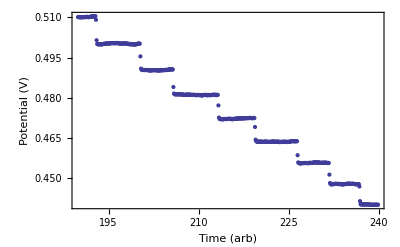

```mathematica
cuvolt=ListPlot[Take[timevolt,{1900,2400}],Frame->True,Axes->False,FrameLabel->{"Time (arb)","Potential (V)"}]
```

```mathematica
Export["cuvolt.eps",cuvolt]
```

cuvolt.eps

```mathematica
threshold=.005;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+3,i+7}]][[1]]}}]}],{i,num-7}]
```

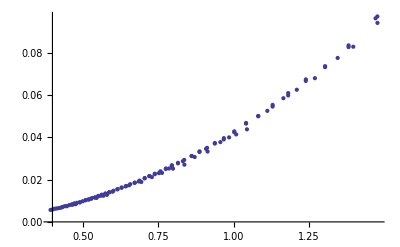

```mathematica
ListPlot[dT]
```

```mathematica
threshold=.005;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{Print[timevolt[[i]]],Print[Mean[Take[voltage,{i-5,i}]]-Mean[Take[voltage,{i+2,i+7}]]],dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+2,i+7}]][[1]]}}]}],{i,num-7}];
```

{3.801,1.47606}

{0.079697}

{3.901,1.47581}

{0.0944675}

{4.001,1.46968}

{0.0959837}

{4.101,1.39596}

{0.0827917}

{7.601,1.38038}

{0.0749322}

{7.701,1.38039}

{0.0829167}

{7.801,1.34428}

{0.0774922}

{12.701,1.30259}

{0.0665747}

{12.801,1.30267}

{0.073264}

{12.901,1.26898}

{0.0680365}

{17.801,1.23884}

{0.0605045}

{17.901,1.23901}

{0.0669173}

{18.001,1.20899}

{0.0624488}

{22.501,1.18041}

{0.0524132}

{22.601,1.18058}

{0.0601718}

{22.701,1.16461}

{0.0584092}

{27.101,1.12888}

{0.0482968}

{27.201,1.1291}

{0.0548258}

{27.301,1.11142}

{0.0525068}

{31.001,1.08147}

{0.0477813}

{31.101,1.08119}

{0.0500615}

{31.201,1.04399}

{0.0439083}

{35.201,1.04095}

{0.0440728}

{35.301,1.04097}

{0.0466447}

{35.401,1.00834}

{0.0414397}

{39.001,1.00191}

{0.0380978}

{39.101,1.00212}

{0.0425785}

{39.201,0.984852}

{0.0400458}

{42.901,0.967273}

{0.0342962}

{43.001,0.967513}

{0.0392615}

{43.101,0.955938}

{0.0377912}

{47.601,0.937476}

{0.0347815}

{47.701,0.937895}

{0.0372425}

{47.801,0.913529}

{0.0333742}

{53.601,0.911881}

{0.034273}

{53.701,0.908546}

{0.0345647}

{59.301,0.886733}

{0.0301357}

{59.401,0.887004}

{0.0332223}

{59.501,0.870979}

{0.0307487}

{63.901,0.861234}

{0.0299357}

{64.001,0.86067}

{0.0311498}

{64.101,0.836885}

{0.0271512}

{67.801,0.836183}

{0.0287848}

{67.901,0.831959}

{0.0286955}

{73.801,0.815513}

{0.0257583}

{73.901,0.815677}

{0.0278393}

{74.001,0.799162}

{0.0252548}

{79.501,0.795324}

{0.0235427}

{79.601,0.795438}

{0.0265943}

{79.701,0.785967}

{0.0252932}

{84.701,0.77535}

{0.0228908}

{84.801,0.775538}

{0.0251693}

{84.901,0.762764}

{0.0232168}

{91.001,0.757384}

{0.0203552}

{91.101,0.757486}

{0.0236075}

{91.201,0.752339}

{0.0230997}

{96.401,0.738861}

{0.0203863}

{96.501,0.738909}

{0.022663}

{96.601,0.72915}

{0.021211}

{102.101,0.721432}

{0.0210358}

{102.201,0.720352}

{0.0215812}

{108.901,0.70535}

{0.0189773}

{109.001,0.705506}

{0.020648}

{109.101,0.694291}

{0.0189062}

{113.901,0.688461}

{0.0191395}

{114.001,0.685793}

{0.0191048}

{119.501,0.672904}

{0.0180332}

{119.601,0.671873}

{0.0184297}

{124.501,0.657509}

{0.0175628}

{124.601,0.653895}

{0.017299}

{131.401,0.643786}

{0.0165462}

{131.501,0.642198}

{0.016759}

{137.201,0.628982}

{0.0153907}

{137.301,0.628956}

{0.0161798}

{144.401,0.615598}

{0.0147787}

{144.501,0.615272}

{0.0154105}

{149.601,0.602114}

{0.0144857}

{149.701,0.599109}

{0.0142638}

{154.001,0.58819}

{0.0129255}

{154.101,0.588242}

{0.0139963}

{154.201,0.580451}

{0.0127727}

{158.801,0.575307}

{0.0121667}

{158.901,0.575366}

{0.0133368}

{159.001,0.568733}

{0.0123463}

{162.701,0.563157}

{0.0126972}

{162.801,0.559743}

{0.0123645}

{168.801,0.551741}

{0.011066}

{168.901,0.551829}

{0.0121937}

{169.001,0.546108}

{0.0113478}

{175.501,0.541072}

{0.0110187}

{175.601,0.540829}

{0.0115307}

{181.901,0.530623}

{0.011089}

{182.001,0.528001}

{0.0108578}

{186.601,0.519966}

{0.0097565}

{186.701,0.520053}

{0.0106063}

{192.801,0.510474}

{0.0101145}

{192.901,0.509118}

{0.0101677}

{200.201,0.500185}

{0.00969467}

{205.601,0.490684}

{0.00879233}

{205.701,0.490529}

{0.00924067}

{213.201,0.481078}

{0.008925}

{213.301,0.477164}

{0.008363}

{219.301,0.472429}

{0.00865483}

{219.401,0.469116}

{0.00822017}

{226.301,0.463816}

{0.00767367}

{226.401,0.463803}

{0.008165}

{231.701,0.455693}

{0.0078775}

{236.701,0.447804}

{0.00732683}

{236.801,0.446913}

{0.00738517}

{241.301,0.440142}

{0.0073415}

{246.201,0.432479}

{0.006779}

{246.301,0.431711}

{0.00688133}

{250.801,0.425456}

{0.00655667}

{255.401,0.418248}

{0.00641133}

{260.501,0.412067}

{0.00625417}

{265.501,0.406081}

{0.00608883}

{270.301,0.399715}

{0.00571733}

{275.201,0.393706}

{0.005613}

```mathematica
Q=10.5^2/1116 10^-2;
```

```mathematica
threshold=.002;
```

```mathematica
dT={};
Do[If[temp[[i+2]][[1]]>temp[[i]][[1]]+threshold,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-5,i}]][[1]]+Mean[Take[temp,{i+3,i+7}]][[1]])}}]}],{i,5,num-7}]
```

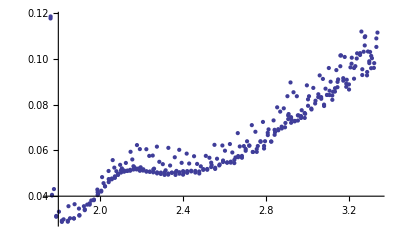

```mathematica
ListPlot[dT]
```

```mathematica
Dimensions[dT]
```

{295,2}

```mathematica
dV=Take[dT,All,{2}];
V=Take[dT,All,{1}];
```

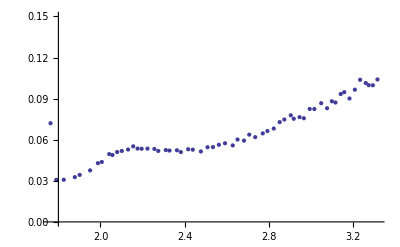

```mathematica
avgsize=5;
avgnum=Quotient[295,avgsize];
avgV=Take[V,{1,-1,avgsize}];
avgdV=Table[0,{i,avgnum}];
Do[avgdV[[i]]=Mean[Take[dV,{1+avgsize(i-1),avgsize(i)}]],{i,1,avgnum}]
avgdT=Table[0,{i,avgnum}];
Do[avgdT[[i]]=Flatten[{avgV[[i]],avgdV[[i]]},2],{i,1,avgnum}]
cu=ListPlot[avgdT,PlotRange->{0,.15},Joined->False]
```

```mathematica
avgdT
```

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
avgdT;
```

```mathematica
NonlinearRegress[avgdT,{AA*T+BB*T^3},{AA,BB},T]
```

{BestFitParameters→{AA→0.0159325,BB→0.00125456},ParameterCITable→ | Estimate | Asymptotic SE | CI
AA | 0.0159325 | 0.00120937 | {0.0135108,0.0183542}
BB | 0.00125456 | 0.000150798 | {0.00095259,0.00155653},EstimatedVariance→0.000047587,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 0.269145 | 0.134573
Error | 57 | 0.00271246 | 0.000047587
Uncorrected Total | 59 | 0.271858 | 
Corrected Total | 58 | 0.0227564 | ,AsymptoticCorrelationMatrix→(1. | -0.959116
-0.959116 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0
Max Parameter-Effects | 0
95. % Confidence Region | 0.562647}

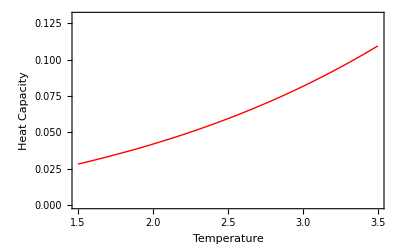

```mathematica
fitcu=Plot[0.015932467940417003*T+0.0012545580454563976*T^3,{T,1.5,3.5},PlotRange->{0,.13},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Temperature","Heat Capacity"}]
```

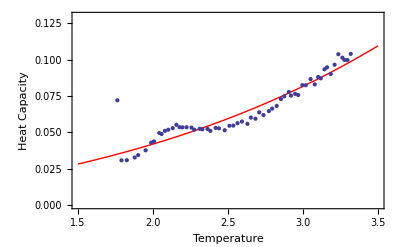

```mathematica
Show[fitcu,cu]
```